```mathematica
<<FeynGrav`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav version 2.0

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

FeynGrav: Examples can be found in FeynGrav_Examples.nb and ArXiV:2201.06812.

Graviton-Fermion vertices are imported up to order 4 in κ.

Graviton-Vector vertices are imported up to order 4 in κ.

Graviton-Massive Vector vertices are imported up to order 4 in κ.

Graviton-Vector-Ghost vertices are imported up to order 4 in κ.

Graviton-Gluon vertices are imported up to order 4 in κ.

Graviton-Three-Gluon vertices are imported up to order 4 in κ.

Graviton-Four-Gluon vertices are imported up to order 4 in κ.

Graviton-Quark-Gluon vertices are imported up to order 4 in κ.

Graviton-(Yang-Mills) Ghost vertices are imported up to order 4 in κ.

Graviton-Gluon-Ghost vertices are imported up to order 4 in κ.

Graviton vertices are imported up to order 3 in κ.

# Scalar-graviton vertices

## Kinetic term

-Graphics-

The trimmed mean evaluation time is 0.00552928 seconds

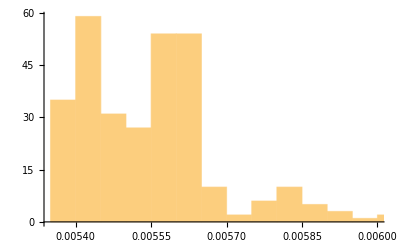

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1},p1,p2,m]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0233246 seconds

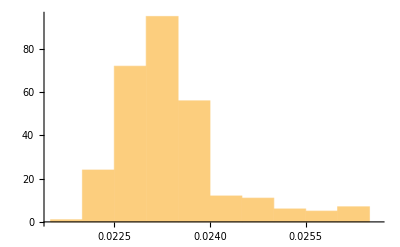

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2},p1,p2,m]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.230217 seconds

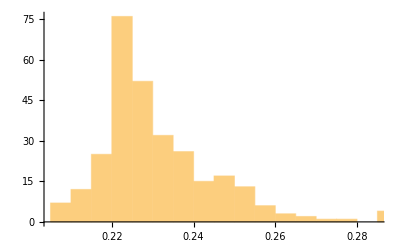

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3},p1,p2,m]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.07731 seconds

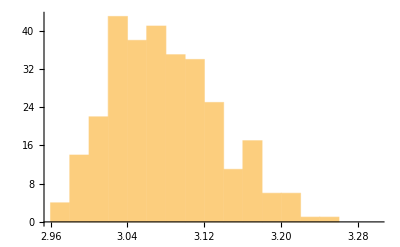

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},p1,p2,m]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## Potential term

-Graphics-

The trimmed mean evaluation time is 0.00071045 seconds

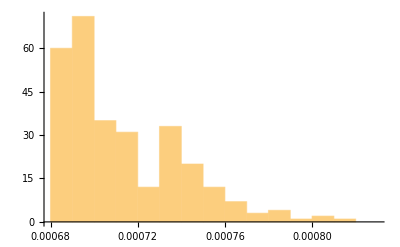

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1},λ]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00115254 seconds

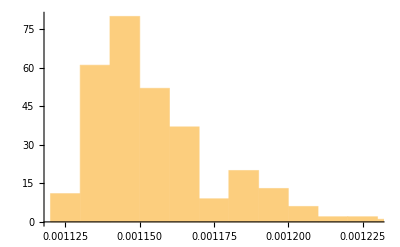

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2},λ]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00569189 seconds

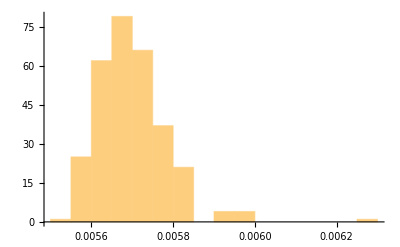

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3},λ]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0869571 seconds

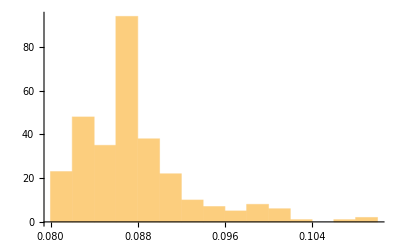

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},λ]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.9571 seconds

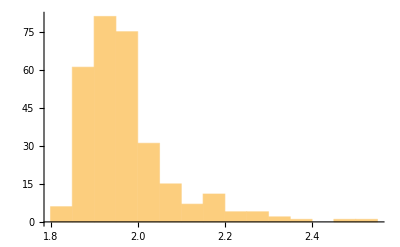

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},λ]][[1]],{n,300}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,301},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,300},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

# Graviton-vector vertices